```mathematica
Clear["`*"]
```

## a.)

```mathematica
xguess = cc1 * Cos[ω t] + cc3* Cos[3ω t];
guess = D[xguess, {t, 2}] + xguess  - 3 * xguess^3 - A * Cos[ω t]//TrigReduce;
collected = Collect[guess, {Cos[3 ω t], Cos[ω t]}];
eq1 = Coefficient[collected, Cos[ω t]]
eq3 = Coefficient[collected, Cos[3ω t]]
```

1/4 (-4 A-9 cc1^3-9 cc1^2 cc3-18 cc1 cc3^2-4 cc1 ω^2+4 cc1)

1/4 (-3 cc1^3-18 cc1^2 cc3-9 cc3^3-36 cc3 ω^2+4 cc3)

## b.)

```mathematica
eq3
c3 = cc3/.(Solve[1/4(-3 cc1^3 - 36cc3 ω^2 + 4cc3)==0, cc3]//FullSimplify)[[1]] (* ∃ better programmatic way to do this? I'd rather not have to hard code function into Solve[] *)
```

1/4 (-3 cc1^3-18 cc1^2 cc3-9 cc3^3-36 cc3 ω^2+4 cc3)

(3 cc1^3)/(4-36 ω^2)

## c.)

```mathematica
eq1/.cc3->c3
coefs = CoefficientList[eq1/.cc3->c3,  cc1];
neweq1 = Sum[cc1^(i - 1) coefs[[i]], {i, 1, 4}]
```

1/4 (-4 A-(162 cc1^7)/((4-36 ω^2)^2)-(27 cc1^5)/(4-36 ω^2)-9 cc1^3-4 cc1 ω^2+4 cc1)

-A-(9 cc1^3)/4+cc1 (1-ω^2)

## d.)

```mathematica
sol = Solve[0==(neweq1/.A->0.136), cc1]//Quiet;
s1 = cc1/. sol[[1]];
s2 = cc1/. sol[[2]];
s3 = cc1/. sol[[3]];
```

## e.) and f.)

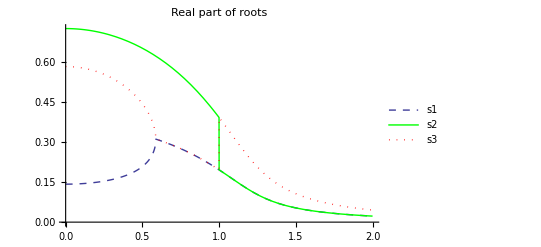

```mathematica
Plot[{Abs[Re[s1]],Abs[Re[s2]],Abs[Re[s3]]}, {ω, 0, 2}, PlotLegends->{"s1", "s2", "s3"}, PlotLabel->"Real part of roots", PlotStyle->{{Dashed, Thick},{Thick, Green},{Dotted, Thick, Red}}]
```

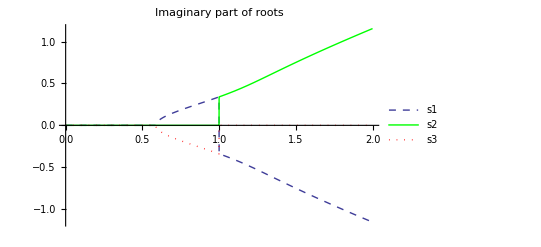

```mathematica
Plot[{Im[s1],Im[s2],Im[s3]}, {ω, 0, 2}, PlotLegends->{"s1", "s2", "s3"}, PlotLabel->"Imaginary part of roots" ,PlotStyle->{{Dashed},{Thick, Green},{Dotted, Thick, Red}}]
```